```mathematica
SetDirectory[NotebookDirectory[]]
```

F:\Dropbox\UNI\Projekte\A02_MCWD_Dataset_Analysis\2021\Analysis\Figure2\VarPET

```mathematica
data05010 =Import["../2005-2010Areas.tsv"];

scens05010 = DeleteDuplicates[Rest[data05010[[All,3]]]]
```

{CHIRPS,CRU NCEP,ERA 5,GLDAS,GPCC,TRMM 6,TRMM 7,GSWP 3,WATCH WFDEI}

```mathematica
data05010VARET =Import["2005-2010Areas_varET.tsv"];
```

```mathematica
data05010VARBSLN=Import["../VarBasetime/2005-2010Areas_var_baseline.tsv"];
```

```mathematica
Select[data05010, #[[3]]== "CHIRPS"&]
```

{{0,2005,CHIRPS,1,2.61815×10^6,0.44043,0.991507,3.82091×10^6,0.642761,3.42201×10^6,0.575656},{1,2005,CHIRPS,2,294171.,0.049486,0.991507,149264.,0.0251094,273510.,0.0460103},{2,2005,CHIRPS,3,101621.,0.0170949,0.991507,6056.03,0.00101876,18411.7,0.00309725},{0,2010,CHIRPS,1,3.14826×10^6,0.529606,1.4321,3.27719×10^6,0.551294,3.99391×10^6,0.671862},{1,2010,CHIRPS,2,515921.,0.0867892,1.4321,475295.,0.079955,147003.,0.0247292},{2,2010,CHIRPS,3,79484.8,0.0133711,1.4321,69659.4,0.0117182,6176.33,0.00103899}}

```mathematica
cols = {RGBColor[255/255,185/255,15/255],RGBColor[205/255,149/255,12/255], RGBColor[165/255,42/255,42/255]}
```

{RGBColor[1, Rational[37, 51], Rational[1, 17]],RGBColor[Rational[41, 51], Rational[149, 255], Rational[4, 85]],RGBColor[Rational[11, 17], Rational[14, 85], Rational[14, 85]]}

```mathematica
sLenged = SwatchLegend[cols,Reverse@{"extreme   \t(x < -2.5)","severe     \t(-2.5 < x < -2)","moderate\t(-2 < x < -0.5)"}, LabelStyle->Directive[14, Black, FontFamily->"Arial"], LegendLabel->"Relative MCWD anomaly (r)", LegendLayout->"Column"]
```

```mathematica
chartData05 = Partition[Select[data05010,#[[2]]==2005&][[All,5]]/10^6,3];
chartData05Rel = Partition[Select[data05010,#[[2]]==2005&][[All,6]]*100,3]
chartData05RelVarPET = Partition[Select[data05010VARET,#[[2]]==2005&][[All,6]]*100,3]
chartData05RelVarBSLN = Partition[Select[data05010VARBSLN,#[[2]]==2005&][[All,6]]*100,3]

chartData05DiffRelPET =chartData05RelVarPET- chartData05Rel;
chartData05DiffRelBSLN=chartData05RelVarBSLN- chartData05Rel;

chartData05 = Table[Reverse[chartData05[[j]]],{j, 1, Length@chartData05}];
chartData05Rel = Table[Reverse[chartData05Rel[[j]]],{j, 1, Length@chartData05}];
```

{{44.043,4.9486,1.70949},{40.4449,7.78808,2.63745},{33.1503,1.96657,1.44883},{37.565,6.35284,2.53743},{37.3579,6.74631,2.22491},{40.2232,3.96426,0.725479},{37.6101,4.84339,2.12354},{34.6491,7.10763,2.01896},{35.0613,7.10892,2.32765}}

{{29.9906,2.36758,1.08452},{30.241,3.1932,2.11712},{22.6376,1.44594,0.464788},{26.7874,2.58001,2.01573},{29.5655,2.37606,1.8612},{28.7663,1.83982,0.927769},{27.4012,1.91113,1.24245},{28.02,2.73776,1.9121},{29.1891,2.53084,2.32725}}

{{42.407,4.46668,1.80983},{34.3251,6.05717,14.802},{40.7935,4.11171,1.85876},{35.0806,6.74669,8.71238},{38.571,5.94306,14.8969},{41.2055,5.60388,1.44553},{38.5261,4.82989,4.4835},{39.7971,5.19782,8.27376},{39.4791,4.42737,8.48037}}

```mathematica
chartData05DiffRelPET
```

{{-14.0524,-2.58102,-0.624963},{-10.2039,-4.59488,-0.520326},{-10.5128,-0.520632,-0.984042},{-10.7776,-3.77283,-0.5217},{-7.79232,-4.37025,-0.363709},{-11.4569,-2.12444,0.202289},{-10.2088,-2.93226,-0.881087},{-6.62909,-4.36987,-0.10686},{-5.8722,-4.57808,-0.000398452}}

```mathematica
chartData05DiffRelBSLN
```

{{-1.63599,-0.481927,0.100342},{-6.11985,-1.73091,12.1645},{7.64313,2.14514,0.409927},{-2.48441,0.393852,6.17495},{1.21311,-0.803248,12.672},{0.982321,1.63962,0.720046},{0.916075,-0.0135022,2.35995},{5.14806,-1.90981,6.2548},{4.4178,-2.68155,6.15272}}

```mathematica
labs = Rotate[Style[#,14, FontFamily->"Arial"], 90°]&/@scens05010
```

{CHIRPS,CRU NCEP,ERA 5,GLDAS,GPCC,TRMM 6,TRMM 7,GSWP 3,WATCH WFDEI}

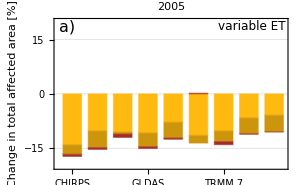

```mathematica
l1a= BarChart[chartData05DiffRelPET,ChartLabels->{labs, None}, ChartLayout->"Stacked", LabelStyle->Directive[12, Black, FontFamily->"Arial"], BarSpacing->0.35, ChartStyle->cols, FrameLabel->{"","Change in\ntotal affected area [%]", None, None}, Frame->True, PlotLabel->"2005", PlotRange->{-20,20}, ImageSize->300, GridLines->Automatic, Epilog->{Inset[Style["a)",16] ,{0.8,18.5}],Inset[Style["variable ET",12] ,{8.1,18.5}]},ImagePadding->{{60,10},{105,10}}]
```

```mathematica
5
```

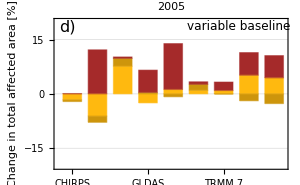

```mathematica
l1b = BarChart[chartData05DiffRelBSLN,ChartLabels->{labs, None}, ChartLayout->"Stacked", LabelStyle->Directive[12, Black, FontFamily->"Arial"], BarSpacing->0.35, ChartStyle->cols, FrameLabel->{"","Change in\ntotal affected area [%]", None, None}, Frame->True, PlotLabel->"2005", PlotRange->{-20,20}, ImageSize->300, GridLines->Automatic,  Epilog->{Inset[Style["d)",16] ,{0.8,18.5}],
Inset[Style["variable baseline",12] ,{7.6,18.5}]},ImagePadding->{{60,10},{105,10}}]
```

```mathematica
chartData05 = Partition[Select[data05010,#[[2]]==2010&][[All,5]]/10^6,3];
chartData05Rel = Partition[Select[data05010,#[[2]]==2010&][[All,6]]*100,3];
chartData05RelVarPET = Partition[Select[data05010VARET,#[[2]]==2010&][[All,6]]*100,3];
chartData05RelVarBSLN = Partition[Select[data05010VARBSLN,#[[2]]==2010&][[All,6]]*100,3];

chartData10DiffRelPET =chartData05RelVarPET- chartData05Rel
chartData10DiffRelBSLN=chartData05RelVarBSLN- chartData05Rel
```

{{-16.5118,1.10784,0.290697},{-9.01447,3.6435,-1.79287},{-18.4552,-1.61654,-0.428652},{-12.0219,3.3047,-1.86077},{-5.54698,1.89517,-2.54797},{-17.8318,-1.80355,-0.632869},{-14.8107,1.5828,-1.71337},{-7.90565,2.20053,-2.65063},{-7.97544,2.14805,-2.44136}}

{{-7.57771,-1.3301,4.44485},{-2.76736,4.13022,8.2969},{-11.2735,2.75655,9.50574},{-1.10933,-1.07178,7.06822},{-3.60509,1.38877,9.38168},{-0.0293925,1.47243,2.32401},{-2.34261,2.16331,1.4196},{-4.94408,4.12471,2.29517},{-3.26333,2.58656,0.765451}}

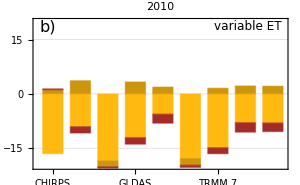

```mathematica
l2a =BarChart[chartData10DiffRelPET,ChartLabels->{labs, None}, ChartLayout->"Stacked", LabelStyle->Directive[12, Black, FontFamily->"Arial"], BarSpacing->0.35, ChartStyle->cols, FrameLabel->{"","", None, None}, Frame->True, PlotLabel->"2010", PlotRange->{-20,20}, ImageSize->300, GridLines->Automatic,  Epilog->{Inset[Style["b)",16] ,{0.8,18.5}],Inset[Style["variable ET",12] ,{8.1,18.5}]},ImagePadding->{{60,10},{105,10}}]
```

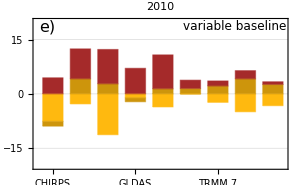

```mathematica
l2b =BarChart[chartData10DiffRelBSLN,ChartLabels->{labs, None}, ChartLayout->"Stacked", LabelStyle->Directive[12, Black, FontFamily->"Arial"], BarSpacing->0.35, ChartStyle->cols, FrameLabel->{"","", None, None}, Frame->True, PlotLabel->"2010", PlotRange->{-20,20}, ImageSize->300, GridLines->Automatic,  Epilog->{Inset[Style["e)",16] ,{0.8,18.5}],
Inset[Style["variable baseline",12] ,{7.6,18.5}]},ImagePadding->{{60,10},{105,10}}]
```

```mathematica
data0501016 =Import["../2005-2010-2016Areas.tsv"];
data0501016varet =Import["2005-2010-2016Areas_VARET.tsv"];
data0501016VARBSLN=Import["../VarBasetime/2005-2010-2016Areas_var_baseline.tsv"];

scens0501016 = DeleteDuplicates[Rest[data0501016[[All,3]]]]
```

{CHIRPS,CRU NCEP,ERA 5,GLDAS,TRMM 7,GPCC}

```mathematica
labs16= Rotate[Style[#,14, FontFamily->"Arial"], 90°]&/@scens0501016
```

{CHIRPS,CRU NCEP,ERA 5,GLDAS,TRMM 7,GPCC}

```mathematica
chartData05 = Partition[Select[data0501016,#[[2]]==2016&][[All,5]]/10^6,3];
chartData05Rel = Partition[Select[data0501016,#[[2]]==2016&][[All,6]]*100,3]
chartData05RelVarPET = Partition[Select[data0501016varet,#[[2]]==2016&][[All,6]]*100,3]
chartData05RelVarBSLN = Partition[Select[data0501016VARBSLN,#[[2]]==2016&][[All,6]]*100,3]

chartData16DiffRelPET =chartData05RelVarPET- chartData05Rel;
chartData16DiffRelBSLN=chartData05RelVarBSLN- chartData05Rel;
```

{{23.9757,7.10725,6.73747},{27.5372,6.27982,4.20617},{24.9189,8.10026,9.66354},{41.4979,8.68602,12.6582},{33.8637,6.05496,7.8287},{37.4793,4.89668,7.67199}}

{{18.4852,5.64396,5.63941},{20.7297,4.01117,4.20856},{18.8389,5.75515,6.23184},{31.0912,4.61337,6.02555},{24.3478,5.84095,6.5299},{25.9757,4.89736,5.50391}}

{{26.1172,6.53789,3.99311},{34.8294,5.01404,8.98426},{39.2385,6.79679,9.24657},{41.4979,8.68602,12.6582},{34.9309,6.71567,8.65844},{43.4885,7.70935,11.0441}}

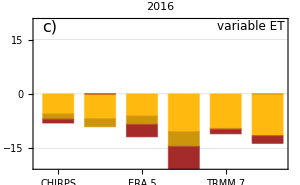

```mathematica
l3a=BarChart[chartData16DiffRelPET,ChartLabels->{labs16, None}, ChartLayout->"Stacked",ChartLegends->None, LabelStyle->Directive[12, Black, FontFamily->"Arial"], BarSpacing->0.35, ChartStyle->cols, FrameLabel->{"",""}, Frame->True, PlotLabel->"2016", PlotRange->{-20,20}, ImageSize->300, GridLines->Automatic,  Epilog-> {Inset[Style["c)",16] ,{0.8,18.5}],Inset[Style["variable ET",12] ,{5.6,18.5}]},ImagePadding->{{60,10},{105,10}}]
```

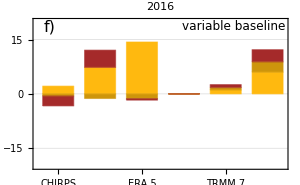

```mathematica
l3b=BarChart[chartData16DiffRelBSLN,ChartLabels->{labs16, None}, ChartLayout->"Stacked",ChartLegends->None, LabelStyle->Directive[12, Black, FontFamily->"Arial"], BarSpacing->0.35, ChartStyle->cols, FrameLabel->{"",""}, Frame->True, PlotLabel->"2016", PlotRange->{-20,20}, ImageSize->300, GridLines->Automatic,Epilog->{Inset[Style["f)",16] ,{0.8,18.5}],
Inset[Style["variable baseline",12] ,{5.2,18.5}]},ImagePadding->{{60,10},{105,10}}]
```

```mathematica
grd = Grid[{{l1a,l2a,l3a},{l1b,l2b,l3b},{sLenged,SpanFromLeft}}, Spacings->{-0.1, 0}]
```

-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
 |  |

```mathematica
Export["Figure2SI.png",grd, ImageResolution-> 300]
```

Figure2SI.png

```mathematica
accChart05 =Accumulate[chartData05[[#]]]&/@Range[scens05010//Length];
accChart10 =Accumulate[chartData10[[#]]]&/@Range[scens05010//Length];
accChart16 =Accumulate[chartData16[[#]]]&/@Range[scens0501016//Length];zSD[data_]:= StandardDeviation[data/(Max[data]-Min[data])-Min[data]/(Max[data]-Min[data])]
```

```mathematica
accLables = {"< -2.5", "< -2", "< -0.5"};
```

```mathematica
p[data_]:= Table[ToString@Round[data[[i,j]],0.1]<> "(" <> ToString@Round[data[[i,j]]/5.94*100] <>"%)",{i, 1, Length[data]},{j,1,3}]
```

```mathematica
Table[ToString@Round[accChart05[[i,j]],0.01]<> "(" <> ToString@Round[accChart05[[i,j]]/5.94*100] <>"%)",{i, 1, Length[accChart05]},{j,1,3}]
```

{{0.1(2%),0.4(7%),3.01(51%)},{0.16(3%),0.62(10%),3.02(51%)},{0.09(1%),0.2(3%),2.17(37%)},{0.15(3%),0.53(9%),2.76(46%)},{0.13(2%),0.53(9%),2.75(46%)},{0.04(1%),0.28(5%),2.67(45%)},{0.13(2%),0.41(7%),2.65(45%)},{0.12(2%),0.54(9%),2.6(44%)},{0.14(2%),0.56(9%),2.65(45%)}}

```mathematica
TableForm[p[accChart05], TableHeadings->{scens05010, accLables}]
```

| < -2.5 | < -2 | < -0.5
CHIRPS | 0.1(2%) | 0.4(7%) | 3.(51%)
CRU NCEP | 0.2(3%) | 0.6(10%) | 3.(51%)
ERA 5 | 0.1(1%) | 0.2(3%) | 2.2(37%)
GLDAS | 0.2(3%) | 0.5(9%) | 2.8(46%)
GPCC | 0.1(2%) | 0.5(9%) | 2.8(46%)
TRMM 6 | 0.(1%) | 0.3(5%) | 2.7(45%)
TRMM 7 | 0.1(2%) | 0.4(7%) | 2.6(45%)
GSWP 3 | 0.1(2%) | 0.5(9%) | 2.6(44%)
WATCH WFDEI | 0.1(2%) | 0.6(9%) | 2.6(45%)

```mathematica
3.0/2.2
```

1.36364

```mathematica
TableForm[an[accChart05], TableHeadings->{accLables,  {Min, Max, Mean,Median, StandardDeviation,zSD}}]
```

| Min | Max | Mean | Median | StandardDeviation | zSD
< -2.5 | 0.(1%) | 0.2(3%) | 0.1(2%) | 0.1(2%) | 0.(1%) | 0.3(5%)
< -2 | 0.2(3%) | 0.6(10%) | 0.5(8%) | 0.5(9%) | 0.1(2%) | 0.3(6%)
< -0.5 | 2.2(37%) | 3.(51%) | 2.7(45%) | 2.7(45%) | 0.3(4%) | 0.3(5%)

```mathematica
TableForm[p[accChart10], TableHeadings->{scens05010, accLables}]
```

| < -3 | < -2 | < -0.5
CHIRPS | 0.(0%) | 0.6(10%) | 3.7(63%)
CRU NCEP | 0.(0%) | 0.3(6%) | 3.4(58%)
ERA 5 | 0.(1%) | 0.8(14%) | 4.2(70%)
GLDAS | 0.(0%) | 0.9(14%) | 3.6(60%)
GPCC | 0.1(1%) | 0.6(9%) | 3.(51%)
TRMM 6 | 0.(0%) | 0.7(12%) | 4.4(74%)
TRMM 7 | 0.1(1%) | 0.5(9%) | 3.8(64%)
GSWP 3 | 0.1(1%) | 0.5(8%) | 3.2(54%)
WATCH WFDEI | 0.1(1%) | 0.4(7%) | 3.1(51%)

```mathematica
Round[61 / 45, 0.01]
```

1.36

```mathematica
Round[10 / 8, 0.01]
```

1.25

```mathematica
TableForm[an[accChart10], TableHeadings->{accLables,  {Min, Max, Mean,Median, StandardDeviation,zSD}}]
```

| Min | Max | Mean | Median | StandardDeviation | zSD
< -3 | 0.(0%) | 0.1(1%) | 0.(1%) | 0.(1%) | 0.(1%) | 0.4(7%)
< -2 | 0.3(6%) | 0.9(14%) | 0.6(10%) | 0.6(9%) | 0.2(3%) | 0.3(6%)
< -0.5 | 3.(51%) | 4.4(74%) | 3.6(61%) | 3.6(60%) | 0.5(8%) | 0.3(6%)

```mathematica
TableForm[an[accChart10-accChart05], TableHeadings->{accLables,  {Min, Max, Mean,Median, StandardDeviation,zSD}}]
```

| Min | Max | Mean | Median | StandardDeviation | zSD
< -3 | 0.(0%) | 0.1(1%) | 0.(1%) | 0.(0%) | 0.(1%) | 0.4(6%)
< -2 | -0.3(-5%) | 0.6(10%) | 0.1(2%) | 0.1(2%) | 0.3(5%) | 0.3(5%)
< -0.5 | 0.3(5%) | 2.(33%) | 0.9(15%) | 0.7(12%) | 0.6(10%) | 0.3(6%)

```mathematica
TableForm[p[accChart16], TableHeadings->{scens0501016, accLables}]
```

| < -3 | < -2 | < -0.5
CHIRPS | 0.1(2%) | 0.8(14%) | 2.2(38%)
CRU_NCEP | 0.1(1%) | 0.6(10%) | 2.3(38%)
ERA 5 | 0.2(4%) | 1.1(18%) | 2.5(43%)
GLDAS | 0.4(6%) | 1.3(21%) | 3.7(63%)
TRMM | 0.2(3%) | 0.8(14%) | 2.8(48%)
GPCC | 0.3(5%) | 0.7(13%) | 3.(50%)

```mathematica
TableForm[an[accChart16], TableHeadings->{accLables,  {Min, Max, Mean,Median, StandardDeviation,zSD}}]
```

| Min | Max | Mean | Median | StandardDeviation | zSD
< -150mm | 0.3(5%) | 1.1(18%) | 0.5(9%) | 0.4(7%) | 0.3(5%) | 0.4(6%)
< -100mm | 0.7(11%) | 1.8(30%) | 1.2(20%) | 0.9(15%) | 0.5(8%) | 0.4(7%)
< -25mm | 2.4(40%) | 4.1(69%) | 3.2(55%) | 3.2(54%) | 0.7(11%) | 0.4(6%)

```mathematica
an[data_]:=  Table[ToString@Round[#@data[[All,i]],0.1]<> "(" <> ToString@Round[#@data[[All,i]]/5.94*100] <>"%)"&/@{Min, Max, Mean, Median, StandardDeviation,zSD},{i,1,3}]
```

```mathematica
Table[ToString@Round[#@accChart05[[All,i]],0.1]<> "(" <> ToString@Round[#@accChart05[[All,i]]/5.94*100] <>"%)"&/@{Min, Max, Mean, Median, StandardDeviation,zSD},{i,1,3}]
```

{{0.(0%),0.(0%),0.(0%),0.(0%),0.(0%),0.3(6%)},{0.2(3%),0.6(10%),0.5(8%),0.5(9%),0.1(2%),0.3(6%)},{2.2(37%),3.(51%),2.7(45%),2.7(45%),0.3(4%),0.3(5%)}}

```mathematica
TableForm[an[accChart05], TableHeadings->{accLables,  {Min, Max, Mean,Median, StandardDeviation,zSD}}]
```

| Min | Max | Mean | Median | StandardDeviation | zSD
< -3 | 0.(0%) | 0.(0%) | 0.(0%) | 0.(0%) | 0.(0%) | 0.3(6%)
< -2 | 0.2(3%) | 0.6(10%) | 0.5(8%) | 0.5(9%) | 0.1(2%) | 0.3(6%)
< -0.5 | 2.2(37%) | 3.(51%) | 2.7(45%) | 2.7(45%) | 0.3(4%) | 0.3(5%)

```mathematica
TableForm[an[accChart10], TableHeadings->{accLables,  {Min, Max, Mean,Median, StandardDeviation,zSD}}]
```

| Min | Max | Mean | Median | StandardDeviation | zSD
< -3 | 0.(0%) | 0.1(1%) | 0.(1%) | 0.(1%) | 0.(1%) | 0.4(7%)
< -2 | 0.3(6%) | 0.9(14%) | 0.6(10%) | 0.6(9%) | 0.2(3%) | 0.3(6%)
< -0.5 | 3.(51%) | 4.4(74%) | 3.6(61%) | 3.6(60%) | 0.5(8%) | 0.3(6%)

```mathematica
TableForm[an[accChart16], TableHeadings->{accLables,  {Min, Max, Mean,Median, StandardDeviation,zSD}}]
```

| Min | Max | Mean | Median | StandardDeviation | zSD
< -3 | 0.1(1%) | 0.4(6%) | 0.2(4%) | 0.2(3%) | 0.1(2%) | 0.4(6%)
< -2 | 0.6(10%) | 1.3(21%) | 0.9(15%) | 0.8(14%) | 0.2(4%) | 0.4(6%)
< -0.5 | 2.2(38%) | 3.7(63%) | 2.8(47%) | 2.7(45%) | 0.6(9%) | 0.4(6%)

```mathematica
TableForm[an[accChart10], TableHeadings->{accLables,  {Min, Max, Mean,Median, StandardDeviation,zSD}}]
```

| Min | Max | Mean | Median | StandardDeviation | zSD
< -3 | 0.(0%) | 0.1(1%) | 0.(1%) | 0.(1%) | 0.(1%) | 0.4(7%)
< -2 | 0.3(6%) | 0.9(14%) | 0.6(10%) | 0.6(9%) | 0.2(3%) | 0.3(6%)
< -0.5 | 3.(51%) | 4.4(74%) | 3.6(61%) | 3.6(60%) | 0.5(8%) | 0.3(6%)

```mathematica
TableForm[an[accChart10-accChart05], TableHeadings->{accLables,  {Min, Max, Mean,Median, StandardDeviation,zSD}}]
```

| Min | Max | Mean | Median | StandardDeviation | zSD
< -3 | 0.(0%) | 0.1(1%) | 0.(1%) | 0.(0%) | 0.(1%) | 0.4(6%)
< -2 | -0.3(-5%) | 0.6(10%) | 0.1(2%) | 0.1(2%) | 0.3(5%) | 0.3(5%)
< -0.5 | 0.3(5%) | 2.(33%) | 0.9(15%) | 0.7(12%) | 0.6(10%) | 0.3(6%)

```mathematica
TableForm[Table[#@accChart05[[All,i]]&/@{Min, Max, Mean,Median, StandardDeviation, zSD},{i,1,3}], TableHeadings->{accLables,  {Min, Max, Mean,Median, StandardDeviation,zSD}}]
TableForm[Table[#@accChart10[[All,i]]&/@{Min, Max, Mean, StandardDeviation, zSD},{i,1,3}], TableHeadings->{accLables,  {Min, Max, Mean, Median, StandardDeviation,zSD}}]
```

| Min | Max | Mean | Median | StandardDeviation | zSD
< -3 | 0. | 0.0246856 | 0.00650429 | 0.0030877 | 0.00835792 | 0.338575
< -2 | 0.20303 | 0.61975 | 0.452976 | 0.528485 | 0.140197 | 0.336429
< -0.5 | 2.17366 | 3.02401 | 2.69938 | 2.66986 | 0.250813 | 0.294953

| Min | Max | Mean | Median | StandardDeviation
< -3 | 0. | 0.0802495 | 0.0383824 | 0.0328079 | 0.408824
< -2 | 0.338385 | 0.859042 | 0.591325 | 0.174325 | 0.334818
< -0.5 | 3.02459 | 4.36738 | 3.59837 | 0.467506 | 0.34816

```mathematica
TableForm[Table[(#@accChart16[[All,i]]-#@accChart05[[All,i]])&/@{Min, Max, Mean, StandardDeviation, zSD},{i,1,3}], TableHeadings->{accLables,  {DMin, MDax, DMean, DMedian,DStandardDeviation,DSD}}]
TableForm[Table[(#@accChart16[[All,i]]-#@accChart10[[All,i]])&/@{Min, Max, Mean, StandardDeviation, zSD},{i,1,3}], TableHeadings->{accLables,  {DMin, DMax,DMean, DMedian, DStandardDeviation,DzSD}}]
```

| DMin | MDax | DMean | DMedian | DStandardDeviation
< -150mm | 0.295034 | 0.340728 | 0.216657 | 0.0689378 | 0.072235
< -100mm | 0.294551 | 0.439288 | 0.279402 | 0.2141 | 0.157898
< -25mm | -0.400868 | -0.153712 | 0.0843239 | 0.208667 | 0.0778238

| DMin | DMax | DMean | DMedian | DStandardDeviation
< -150mm | 0.156816 | 0.720761 | 0.29516 | 0.201698 | -0.000499752
< -100mm | -0.0700155 | 0.105199 | 0.10711 | 0.204288 | 0.138797
< -25mm | -0.742802 | -0.536311 | -0.485616 | 0.13162 | 0.0353119

```mathematica
TableForm[Round[accChart05, 0.01], TableHeadings->{scens, accLables}]
TableForm[Round[accChart10, 0.01], TableHeadings->{scens, accLables}]
TableForm[Round[accChart16, 0.01], TableHeadings->{scens16, accLables}]
```

0.01 | 0.37 | 3.07
0.73 | 1.33 | 3.12
0.09 | 0.75 | 4.24
0.26 | 1.03 | 3.52
0.27 | 0.85 | 2.76
0.4 | 1. | 2.79
0.45 | 1. | 2.87
0.21 | 0.87 | 3.24
0.25 | 0.72 | 3.02
0.46 | 1.06 | 2.93

0.16 | 0.85 | 3.75
0.16 | 0.73 | 3.61
0.3 | 1.35 | 4.63
0.28 | 0.99 | 3.19
0.14 | 1.09 | 3.85
0.27 | 0.98 | 3.1
0.3 | 1.08 | 3.46
0.35 | 1.67 | 4.52
0.17 | 1.07 | 3.87
0.22 | 0.9 | 3.29

0.37 | 0.79 | 2.36
0.3 | 0.66 | 2.45
0.72 | 1.66 | 4.09
1.07 | 1.77 | 3.77
0.47 | 1.58 | 3.62
0.35 | 0.9 | 3.22
0.44 | 0.89 | 3.2

```mathematica
22/16.
```

1.375